## Ex. 2.1

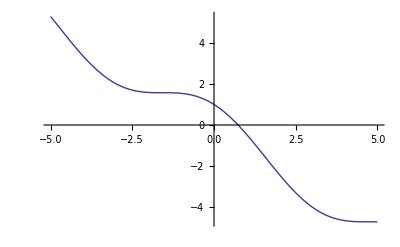

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-x+Cos[x]==0,x]

3.141592654

```mathematica
Plot[Cos[x]-x,{x,-5,5}]
Solve[Cos[x]-x==0,x]
N[Pi,10]
```

## Stepped Well

```mathematica
h=6.582*10^-16
m=0.511*10^6
c=3*10^8
a=10*10^(-10)
b=1*10^(-10)
k=Sqrt[2*m*c^2*x/(h)^2]
q=Sqrt[2*m*c^2/h^2*(x-10)]
```

6.582×10^-16

511000.

300000000

1/1000000000

1/10000000000

4.60775×10^26 √x

4.60775×10^26 √(-10+x)

5 x

5 (-1+x)

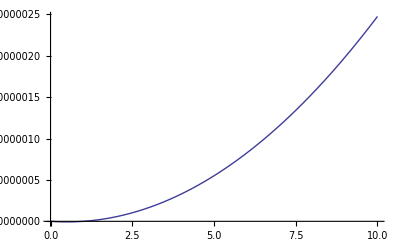

```mathematica
k=5x
q=5(x-1)
Plot[q*Sin[k*a]Cos[q*b]+k Cos[k a]Sin[q b],{x,0,10}]
```

## 2.16

```mathematica
d=6*0.2641
V=10
f[e_]:=(V-2e)Sin[d Sqrt[e]]+2e Sqrt[v/e-1]Cos[d Sqrt[e]]
```

1.5846

10

```mathematica
Plot[f[e],{e,0,1}]
```

Plot::exclul: {Im[v/e] - 0, Im[e] - 0, Im[e] - 0} must be a list of equalities or real-valued functions.

-Graphics-

## Double Well

```mathematica
z=Sqrt[0.2641]
w=6
w2=1
v=10
Pall[x_]:={{Cos[z*Sqrt[x]*w],1/(z*Sqrt[x])Sin[z*Sqrt[x] w]},{-(z*Sqrt[x])Sin[z*Sqrt[x] w],Cos[z*Sqrt[x] w]}}
Pall[x]//MatrixForm
Pfor[x_]:={{Cosh[z*Sqrt[v-x]*w2],1/(z*Sqrt[v-x])Sinh[z*Sqrt[v-x] w2]},{-(z*Sqrt[v-x])Sinh[z*Sqrt[v-x] w2],Cosh[z*Sqrt[v-x] w2]}}
Pfor[x]//MatrixForm
g[x_]:={{1},{z*Sqrt[v-x]}}
g[x]//MatrixForm
```

0.513907

6

1

10

(Cos[3.08344 √x] | (1.94588 Sin[3.08344 √x])/(√x)
-0.513907 √x Sin[3.08344 √x] | Cos[3.08344 √x])

(Cosh[0.513907 √(10-x)] | (1.94588 Sinh[0.513907 √(10-x)])/(√(10-x))
-0.513907 √(10-x) Sinh[0.513907 √(10-x)] | Cosh[0.513907 √(10-x)])

(1
0.513907 √(10-x))

```mathematica
test[x_]:=Pall[x].Pfor[x]
test[x]//MatrixForm
test1[x_]:=test[x].g[x]
test1[x]//MatrixForm
```

(Cos[3.08344 √x] Cosh[0.513907 √(10-x)]-(1. √(10-x) Sin[3.08344 √x] Sinh[0.513907 √(10-x)])/(√x) | (1.94588 Cosh[0.513907 √(10-x)] Sin[3.08344 √x])/(√x)+(1.94588 Cos[3.08344 √x] Sinh[0.513907 √(10-x)])/(√(10-x))
-0.513907 √x Cosh[0.513907 √(10-x)] Sin[3.08344 √x]-0.513907 √(10-x) Cos[3.08344 √x] Sinh[0.513907 √(10-x)] | Cos[3.08344 √x] Cosh[0.513907 √(10-x)]-(1. √x Sin[3.08344 √x] Sinh[0.513907 √(10-x)])/(√(10-x)))

(Cos[3.08344 √x] Cosh[0.513907 √(10-x)]-(1. √(10-x) Sin[3.08344 √x] Sinh[0.513907 √(10-x)])/(√x)+0.513907 √(10-x) ((1.94588 Cosh[0.513907 √(10-x)] Sin[3.08344 √x])/(√x)+(1.94588 Cos[3.08344 √x] Sinh[0.513907 √(10-x)])/(√(10-x)))
-0.513907 √x Cosh[0.513907 √(10-x)] Sin[3.08344 √x]-0.513907 √(10-x) Cos[3.08344 √x] Sinh[0.513907 √(10-x)]+0.513907 √(10-x) (Cos[3.08344 √x] Cosh[0.513907 √(10-x)]-(1. √x Sin[3.08344 √x] Sinh[0.513907 √(10-x)])/(√(10-x))))

```mathematica
ψ1[x_]:=test1[x][[1]]
ψ2[x_]:=test1[x][[2]]
```

```mathematica
ψ2[x]+z Sqrt[v-x]*ψ1[x]
```

{-0.513907 √x Cosh[0.513907 √(10-x)] Sin[3.08344 √x]-0.513907 √(10-x) Cos[3.08344 √x] Sinh[0.513907 √(10-x)]+0.513907 √(10-x) (Cos[3.08344 √x] Cosh[0.513907 √(10-x)]-(1. √x Sin[3.08344 √x] Sinh[0.513907 √(10-x)])/(√(10-x)))+0.513907 √(10-x) (Cos[3.08344 √x] Cosh[0.513907 √(10-x)]-(1. √(10-x) Sin[3.08344 √x] Sinh[0.513907 √(10-x)])/(√x)+0.513907 √(10-x) ((1.94588 Cosh[0.513907 √(10-x)] Sin[3.08344 √x])/(√x)+(1.94588 Cos[3.08344 √x] Sinh[0.513907 √(10-x)])/(√(10-x))))}